Background

```mathematica
coord ={t,r,φ};

metric =({{-f[r], 0, 0}, {0, 1/f[r], 0}, {0, 0, r^2}});
```

```mathematica
$Assumptions= And[t∈Reals,r>0,φ>=0,φ<2π,rh>0,ν>0,L>0];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.Λ ->-(d(d-1))/(2 L^2)/.d->2//Simplify
```

{{f[r] (1/L^2-f'[r]/(2 r)),0,0},{0,(-2 r+L^2 f'[r])/(2 L^2 r f[r]),0},{0,0,(r^2 (-2+L^2 f''[r]))/(2 L^2)}}

```mathematica
EEstep3 = EEstep2/.f->Function[{r},r^2/L^2-rh^2/L^2]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

Perturbation

```mathematica
Φ=1/(√r)Exp[-ⅈ*ω*t]*Exp[ⅈ*J*φ]*ϕ[r]
```

(ⅇ^(ⅈ J φ-ⅈ t ω) ϕ[r])/(√r)

```mathematica
SEstep1 = scalarLaplacian[Φ]-m^2Φ;
SEstep2 = Collect[(SEstep1 √r L^2(r^2-rh^2))/(Exp[-ⅈ*ω*t]Exp[ⅈ*J*φ]),{ϕ''[r],ϕ'[r],ϕ[r]},Simplify]  /. f-> Function[{r},(r^2-rh^2)/L^2] // Simplify
```

-((r^2+L^2 (J^2+m^2 r^2)) (r^2-rh^2) ϕ[r])/r^2+((r^2-rh^2)^2 ϕ[r])/(4 r^2)+L^4 ω^2 ϕ[r]+2 r (r^2-rh^2) ϕ'[r]+(r^2-rh^2)^2 ϕ''[r]

```mathematica
Solution =ϕ[r]/.DSolve[SEstep2==0,ϕ,r][[1]]/. m^2->(ν^2-1)/L^2  /.  C[2]->Subscript[C, 2] /.C[1]->Subscript[C, 1]//Simplify
```

r^(1/2-(ⅈ J L)/rh) (r^2-rh^2)^(-(ⅈ L^2 ω)/(2 rh)) (Hypergeometric2F1[(-ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh),-(ⅈ J L+rh (-1+ν)+ⅈ L^2 ω)/(2 rh),1-(ⅈ J L)/rh,r^2/rh^2] C_1+ⅇ^(-(J L π)/rh) (r/rh)^((2 ⅈ J L)/rh) Hypergeometric2F1[(ⅈ J L+rh-rh ν-ⅈ L^2 ω)/(2 rh),(ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh),1+(ⅈ J L)/rh,r^2/rh^2] C_2)

```mathematica
InftyBehaviour=Asymptotic[Solution,r->Infinity] //FullSimplify
```

-ⅈ ⅇ^(-(π (ⅈ rh ν+L (J+L ω)))/(2 rh)) r^(-1/2-(ⅈ J L)/rh) (r/rh)^(-ν+(ⅈ L (J+L ω))/rh) rh ((r-rh) (r+rh))^(-(ⅈ L^2 ω)/(2 rh)) (Gamma[1-(ⅈ J L)/rh] (Gamma[-ν]/(Gamma[(rh-rh ν+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)])+(ⅇ^(ⅈ π ν) (r/rh)^(2 ν) Gamma[ν])/(Gamma[(rh (1+ν)+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)])) C_1+Gamma[1+(ⅈ J L)/rh] (Gamma[-ν]/(Gamma[(rh-rh ν+ⅈ L (J-L ω))/(2 rh)] Gamma[(rh-rh ν+ⅈ L (J+L ω))/(2 rh)])+(((ⅈ r)/rh)^(2 ν) Gamma[ν])/(Gamma[(rh (1+ν)+ⅈ L (J-L ω))/(2 rh)] Gamma[(rh (1+ν)+ⅈ L (J+L ω))/(2 rh)])) C_2)

```mathematica
Solution = Solution /.Subscript[C, 2]->-Subscript[C, 1]*Gamma[1-(ⅈ J L)/rh]Gamma[(ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh)] Gamma[(rh+rh ν+ⅈ L (J+L ω))/(2 rh)]/(Gamma[(-ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh)] Gamma[(rh+rh ν+ⅈ L (-J+L ω))/(2 rh)]Gamma[1+(ⅈ J L)/rh])
```

r^(1/2-(ⅈ J L)/rh) (r^2-rh^2)^(-(ⅈ L^2 ω)/(2 rh)) (-(ⅇ^(-(J L π)/rh) (r/rh)^((2 ⅈ J L)/rh) Gamma[1-(ⅈ J L)/rh] Gamma[(ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh)] Gamma[(rh+rh ν+ⅈ L (J+L ω))/(2 rh)] Hypergeometric2F1[(ⅈ J L+rh-rh ν-ⅈ L^2 ω)/(2 rh),(ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh),1+(ⅈ J L)/rh,r^2/rh^2] C_1)/(Gamma[1+(ⅈ J L)/rh] Gamma[(-ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh)] Gamma[(rh+rh ν+ⅈ L (-J+L ω))/(2 rh)])+Hypergeometric2F1[(-ⅈ J L+rh+rh ν-ⅈ L^2 ω)/(2 rh),-(ⅈ J L+rh (-1+ν)+ⅈ L^2 ω)/(2 rh),1-(ⅈ J L)/rh,r^2/rh^2] C_1)

```mathematica
BoundaryBehaviour=Series[Solution,{r,rh,0}] //FullSimplify
```

(r-rh)^(-(ⅈ L^2 ω)/(2 rh)) ((-(2^(-(ⅈ L^2 ω)/(2 rh)) ⅇ^(-(J L π)/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-1/2-(ⅈ L (2 J+L ω))/(2 rh)) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh] C_1)/((ⅇ^((J L π)/rh)+ⅇ^(ⅈ π ν+(L^2 π ω)/rh)) Gamma[1-(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh (1+ν)+ⅈ L (-J+L ω))/(2 rh)])+O[r-rh]^1)+(-r+rh)^((ⅈ L^2 ω)/rh) ((2^((ⅈ L^2 ω)/(2 rh)) ⅇ^((L π (-J+L ω))/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-(rh+ⅈ L (2 J+3 L ω))/(2 rh)) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh] C_1)/((ⅇ^(ⅈ π ν)+ⅇ^((L π (J+L ω))/rh)) Gamma[1+(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)])+O[r-rh]^1))

```mathematica
Boundary=Normal[BoundaryBehaviour]
```

(r-rh)^(-(ⅈ L^2 ω)/(2 rh)) (-(2^(-(ⅈ L^2 ω)/(2 rh)) ⅇ^(-(J L π)/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-1/2-(ⅈ L (2 J+L ω))/(2 rh)) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh] C_1)/((ⅇ^((J L π)/rh)+ⅇ^(ⅈ π ν+(L^2 π ω)/rh)) Gamma[1-(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh (1+ν)+ⅈ L (-J+L ω))/(2 rh)])+(2^((ⅈ L^2 ω)/(2 rh)) ⅇ^((L π (-J+L ω))/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-(rh+ⅈ L (2 J+3 L ω))/(2 rh)) (-r+rh)^((ⅈ L^2 ω)/rh) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh] C_1)/((ⅇ^(ⅈ π ν)+ⅇ^((L π (J+L ω))/rh)) Gamma[1+(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)]))

```mathematica
P1=-(((rh)^(-(ⅈ L^2 ω)/(2 rh))2^(-(ⅈ L^2 ω)/(2 rh)) ⅇ^(-(J L π)/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-1/2-(ⅈ L (2 J+L ω))/(2 rh)) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh])/((ⅇ^((J L π)/rh)+ⅇ^(ⅈ π ν+(L^2 π ω)/rh)) Gamma[1-(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh (1+ν)+ⅈ L (-J+L ω))/(2 rh)])) // FullSimplify
```

-(2^(-(ⅈ L^2 ω)/(2 rh)) ⅇ^(-(J L π)/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-1/2-(ⅈ L (J+L ω))/rh) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh])/((ⅇ^((J L π)/rh)+ⅇ^(ⅈ π ν+(L^2 π ω)/rh)) Gamma[1-(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν+ⅈ L (-J+L ω))/(2 rh)] Gamma[(rh (1+ν)+ⅈ L (-J+L ω))/(2 rh)])

```mathematica
Q1=((rh)^((ⅈ L^2 ω)/(2rh))*(-1)^((ⅈ L^2 ω)/rh)2^((ⅈ L^2 ω)/(2 rh)) ⅇ^((L π (-J+L ω))/rh) (-1+ⅇ^((2 J L π)/rh)) J L π rh^(-(rh+ⅈ L (2 J+3 L ω))/(2 rh))Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh])/((ⅇ^(ⅈ π ν)+ⅇ^((L π (J+L ω))/rh)) Gamma[1+(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)])//FullSimplify
```

(2^(1+(ⅈ L^2 ω)/(2 rh)) J L π rh^(-1/2-(ⅈ L (J+L ω))/rh) Csch[(L^2 π ω)/rh] Gamma[-(ⅈ J L)/rh] Sinh[(J L π)/rh])/((ⅇ^(ⅈ π ν)+ⅇ^((L π (J+L ω))/rh)) Gamma[1+(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)])

Checking that indeed Q1 is the same as in the Article

```mathematica
Q1-((-1)^((ⅈ L^2 ω)/rh)2^(1+(ⅈ L^2 ω)/(2 rh)) ⅇ^((2 L^2 π ω)/rh) π^2 rh^(1/2-(ⅈ L^2 ω)/rh-(ⅈ J L)/rh)(Coth[(L^2 π ω)/rh]-1))/((ⅇ^(ⅈ π ν)+ⅇ^((L π (J+L ω))/rh)) Gamma[(ⅈ J L)/rh]Gamma[1+(ⅈ L^2 ω)/rh] Gamma[(rh-rh ν-ⅈ L (J+L ω))/(2 rh)] Gamma[(rh (1+ν)-ⅈ L (J+L ω))/(2 rh)])//FullSimplify
```

0

### Trying to obtain Quantization of Omega

```mathematica
alpha=Arg[P1] /.L->1/.rh->1/.ν->1//FullSimplify
```

Arg[-(2^(-(ⅈ ω)/2) ⅇ^(-J π) (-1+ⅇ^(2 J π)) J Csch[π ω] Gamma[-ⅈ J])/((ⅇ^(J π)-ⅇ^(π ω)) Gamma[1-ⅈ ω] Gamma[1/2 ⅈ (-J+ω)] Gamma[1+1/2 ⅈ (-J+ω)])]

```mathematica
beta=Arg[Q1] /.L->1/.rh->1 /. ν->1 //FullSimplify
```

Arg[(2^(1+(ⅈ ω)/2) J Csch[π ω] Gamma[-ⅈ J] Sinh[J π])/((-1+ⅇ^(π (J+ω))) Gamma[1+ⅈ ω] Gamma[-1/2 ⅈ (J+ω)] Gamma[-1/2 ⅈ (2 ⅈ+J+ω)])]

```mathematica
FindRoot[alpha-beta+20000ω/.J->1,{ω,0.00015}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ω→-1.0188×10^-8}

```mathematica
$MinMachineNumber
```

2.22507×10^-308

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.J->i,{ω,0.00015},WorkingPrecision->100]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ⅇ^(37 π).

General::stop: Further output of N::meprec will be suppressed during this calculation.

General::munfl: 5.54458×10^-305 (2.+0.000103972 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.39603×10^-306 (64.+0.00332711 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.19826×10^-304 (-1.+0.000051986 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

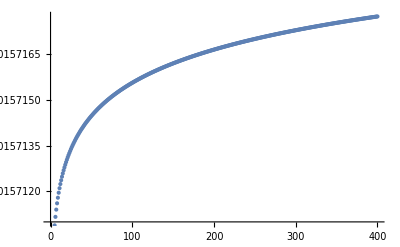

```mathematica
ListPlot[OmegaQuantization]
```

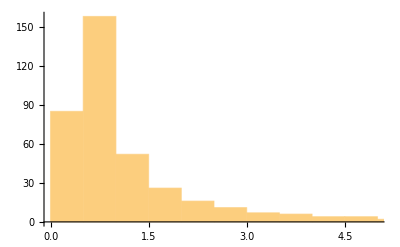

```mathematica
PS = {};
For[i=1, i<=399, i++,
	Value=Abs[OmegaQuantization[[i]]-OmegaQuantization[[i+1]]];
	PS=Append[PS,Value]
]
Histogram[PS]
```

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=400, i++,
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,2/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationtwo=Append[OmegaQuantizationtwo,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(-(ⅈ ω)/2) Csch[π ω] Gamma[-ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[19998.8 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(1+Times[«2»]) Csch[π ω] Gamma[-2 ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-2 ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[20002.1 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(-(ⅈ ω)/2) Csch[π ω] Gamma[-3 ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-3 ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[20002.9 ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::munfl: 5.54458×10^-305 (2.+0.000103972 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.39603×10^-306 (64.+0.00332711 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.19826×10^-304 (-1.+0.000051986 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

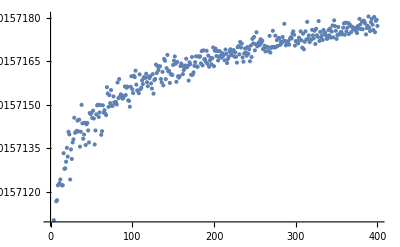

```mathematica
ListPlot[OmegaQuantizationtwo]
```

```mathematica
PS1 = {};
For[i=1, i<=399, i++,
	Value=Abs[OmegaQuantizationtwo[[i]]-OmegaQuantizationtwo[[i+1]]];
	PS1=Append[PS1,Value]
]

Histogram[PS]
```

-Graphics-

```mathematica
OmegaQuantizationthree = {};
For[i=1, i<=400, i++,
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.025/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationthree=Append[OmegaQuantizationthree,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(-(ⅈ ω)/2) Csch[π ω] Gamma[-ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[20000. ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(1+Times[«2»]) Csch[π ω] Gamma[-2 ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-2 ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[20000.1 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (Sin[Arg[-(2^(-(ⅈ ω)/2) Csch[π ω] Gamma[-3 ⅈ])/((Power[«2»]+Times[«2»]) Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Times[«2»]])]-Arg[(2^Plus[«2»] Csch[Times[«2»]] Gamma[-3 ⅈ])/(Plus[«2»] Gamma[«1»] Gamma[«1»] Gamma[«1»])]]=={-Sin[20000. ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::munfl: 5.54458×10^-305 (2.+0.000103972 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.39603×10^-306 (64.+0.00332711 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.19826×10^-304 (-1.+0.000051986 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

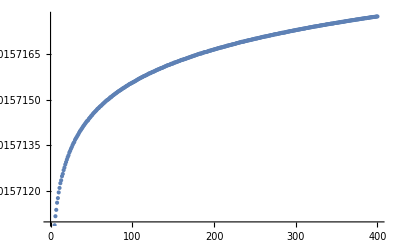

```mathematica
ListPlot[OmegaQuantizationthree]
```

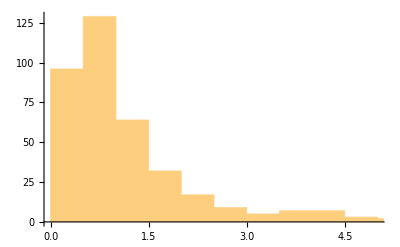

```mathematica
PS2 = {};
For[i=1, i<=399, i++,
	Value=Abs[OmegaQuantizationthree[[i]]-OmegaQuantizationthree[[i+1]]];
	PS2=Append[PS2,Value]
]

Histogram[PS2]
```